# Propiedades electrónicas del grafeno

El grafeno está hecho de átomo de carbono dispuestos en estructura hexagonal.  Los vectores de la red están dados por

OverVector[a_1]= a/2(3, √3), OverVector[a_2]  = a/2(3, - √3)

```mathematica
UnitCell[x_,y_] := {Gray,Line[{{x,y},{x,y+2/3 Sin[120 Degree]}}],
				                Line[{{x,y},{x+Cos[30 Degree]/2,y-Sin[30 Degree]/2}}],
				                Line[{{x,y},{x-Cos[30 Degree]/2,y-Sin[30 Degree]/2}}],
				    Blue,Disk[{x,y},0.1],
				    Red,Disk[{x,y+2/3 Sin[120 Degree]},0.1] } ;
```

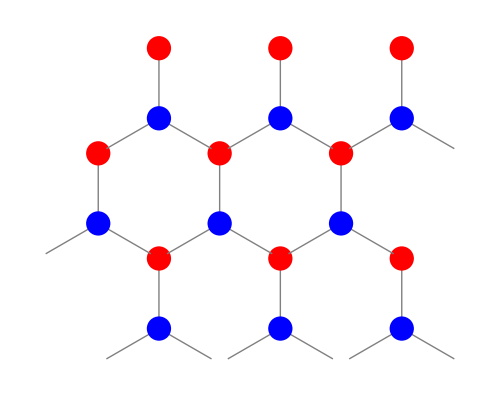

```mathematica
Graphics[Block[{unitVectA={Cos[120 Degree],Sin[120 Degree]},unitVectB={1,0}},Table[UnitCell@@(unitVectA j+unitVectB k),{j,1,3},{k,Ceiling[j/2],2+Ceiling[j/2]}]],ImageSize->500]
```

```mathematica
f[x_, y_] :=2  Cos[√3  y]+4 Cos[(√3)/2  y] Cos[3/2 x]
Energy[x_,y_, n_] :=  n 2.7 √(3+f[x,y]) +0.2 2.7 f[x,y]

Plot3D[{Energy[x,y, 1], Energy[x,y, -1]}, {x, -4,4}, {y,-3,3}]
```

-Graphics3D-